# Spiral Scanning Signal Generation

### Frequencies

```mathematica
Subscript[ω, drive] = 20;
Subscript[ω, mod] = 1;
```

```mathematica
u1 = Sin[Subscript[ω, mod]*t]Sin[Subscript[ω, drive]*t];
u2 = Sin[Subscript[ω, mod]*t]Cos[Subscript[ω, drive]*t];
```

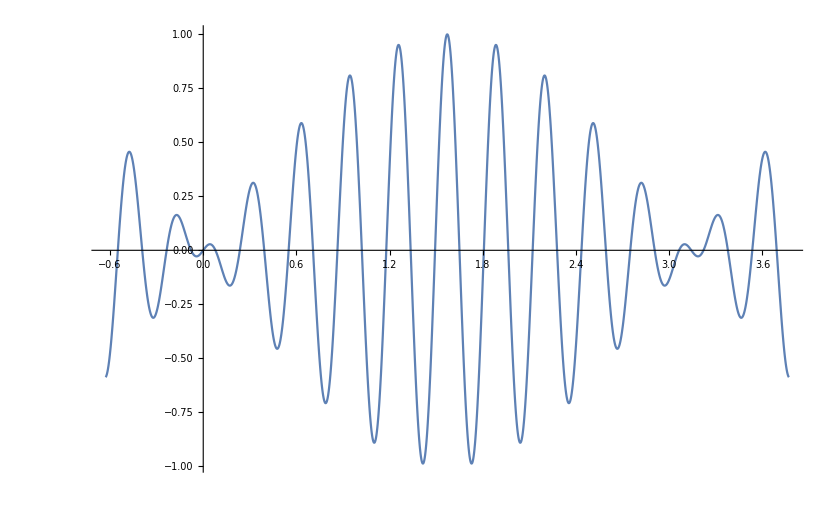

```mathematica
Plot[{u2},{t,-Pi/5,Pi+Pi/5}]
```

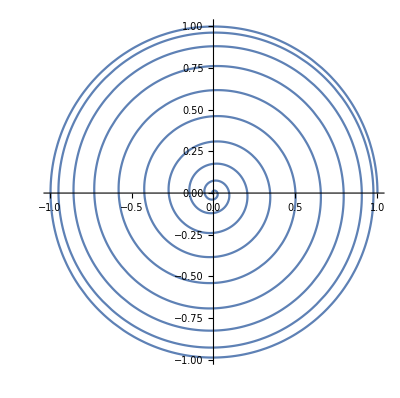

```mathematica
PolarPlot[0.5+0.5*Cos[0.05t],{t,0,20Pi}]
```